```mathematica
rho=1+Max[Cos[t],Cos[t+2 Pi/3],Cos[t-2 Pi/3]]
```

1+Max[Cos[t],-Sin[π/6-t],-Sin[π/6+t]]

```mathematica
f[t_]=Cos[t]/rho;
```

```mathematica
g[t_]=Sin[t]/rho;
```

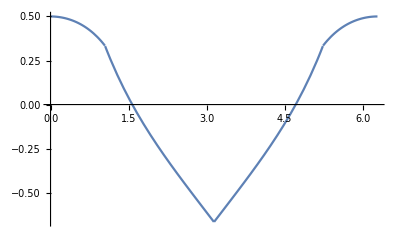

```mathematica
Plot[f[x],{x,0,2*Pi}]
```

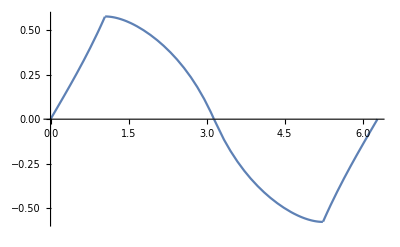

```mathematica
Plot[g[x],{x,0,2*Pi}]
```

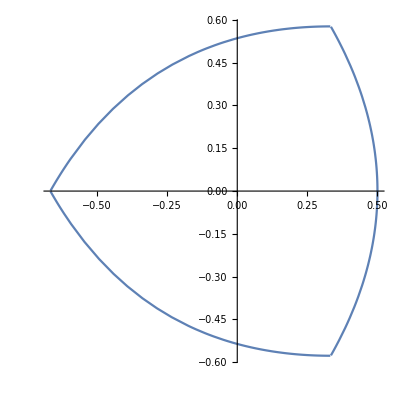

```mathematica
ParametricPlot[{f[t],g[t]},{t,0,2*Pi}]
```